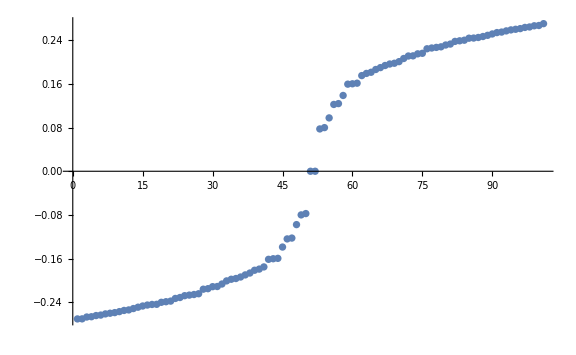

{{1,8},{1,9},{1,10},{1,11},{1,12},{1,13},{1,14},{1,15},{1,16},{1,32},{1,33},{1,34},{1,35},{1,36},{1,37},{1,38},{1,39},{1,40}}

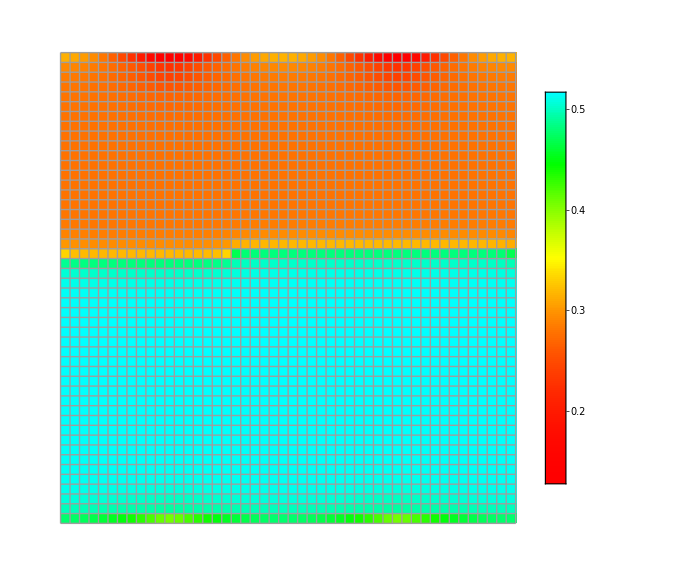

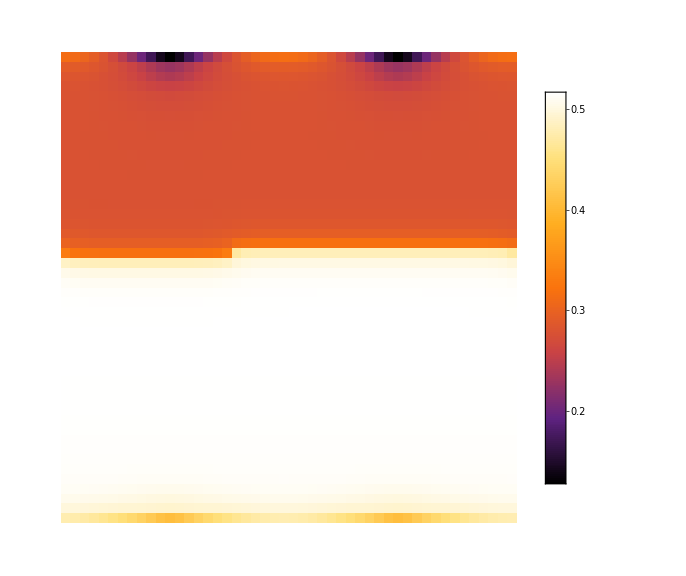

```mathematica
SetDirectory["F:\\Code\\VSProject\\bdg\\bdg\\"];
xn=48;yn=48;
energy = Flatten[Import["energy.dat"]];
del = Flatten[Import["order_module.dat"]];
g1=Flatten[Import["gamma1.dat"]];
g11=ArrayReshape[g1,{xn,yn}];
g2=Flatten[Import["gamma2.dat"]];
g22=ArrayReshape[g2,{xn,yn}];
Export["g1.dat",g11];
Export["g2.dat",g22];
ListPlot[energy[[Round[Length[energy]/2]-50;;Round[Length[energy]/2]+50]],ImageSize->Large]
del2=ArrayReshape[del,{xn,yn}];
Export["del.dat",del2];
Position[del2,n_/;n<(Min[del2]+0.1)]
ArrayPlot[del2,ColorFunction->(Hue[#^2/2]&),PlotLegends->Automatic,PlotTheme->"Detailed",ImageSize->Large,Mesh->All]
ArrayPlot[del2,ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotTheme->"Detailed",ImageSize->Large]
```